```mathematica
Exit
```

```mathematica
Needs["PM`"];
LoadPackages["Geometries"]
```

WARNING: LTemplate has not yet been tested with Mathematica 13.2.1.
The latest supported Mathematica version is 12.3.1.
Please report any issues you find to szhorvat at gmail.com.

```mathematica
M=FigureEightMesh[6];
ClearAll[A,P]
Amat=WeakLaplacian[M]+Mass[M];
A[x_]:=Amat.x;
(*P[x_]:=Mass[M].x;*)
ilu=SparseArray`SparseMatrixILU[Amat];
P[x_]:=SparseArray`SparseMatrixApplyILU[ilu,x];
(*P[x_]:=x;*)

(*b=Mass[M].RandomReal[{-1,1},VertexCount[M]];*)
b=Mass[M].SmoothedRandomVector[M][[All,1]];
n=VertexCount[M];

M1=Displace[M,0.095SmoothedRandomVector[M]];
Amat1=WeakLaplacian[M1]+Mass[M1];
P=LinearSolve[Amat1];
```

```mathematica
MeshPlot[M1]
```

BoundaryStrata::nomatch: No matching first point found.

-Graphics3D-

```mathematica
maxiter=60;
TOL=10^-6;

xTrue=LinearSolve[Amat,b];
ClearAll[error];
error[x_]:=With[{δx=x-xTrue}, Sqrt[Dot[A[δx],δx]]/Sqrt[Dot[A[xTrue],xTrue]]];

resultLeft=GMRES[A,b,
"MaxIterations"->maxiter,
"Tolerance"->TOL,
"GramSchmidtIterations"->1,
"PreconditionerSide"->Left,
"Preconditioner"->P
];//AbsoluteTiming
xLeft=resultLeft["Solution"];
(*Norm[A[xLeft]-b]/Norm[b]*)
Norm[P[A[xLeft]-b]]/Norm[P[b]]
error[xLeft]
```

LinearSolve::lslc: Coefficient matrix and target vector(s) or matrix do not have the same dimensions.

{0.00001,Null}

Norm[{{1.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,1.}}[{{-0.966367+{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}}[GMRES[{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}},{{0.966367},{-0.535376},{-0.827151},{0.99977},{-0.298794},{0.418707},{-0.0865339},{0.127861}},MaxIterations→60,Tolerance→1/1000000,GramSchmidtIterations→1,PreconditionerSide→Left,Preconditioner→{{1.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,1.}}][Solution]]},{0.535376+{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}}[GMRES[{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}},{{0.966367},{-0.535376},{-0.827151},{0.99977},{-0.298794},{0.418707},{-0.0865339},{0.127861}},MaxIterations→60,Tolerance→1/1000000,GramSchmidtIterations→1,PreconditionerSide→Left,Preconditioner→{{1.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,1.}}][Solution]]},{0.827151+{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}}[GMRES[{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}},{{0.966367},{-0.535376},{-0.827151},{0.99977},{-0.298794},{0.418707},{-0.0865339},{0.127861}},MaxIterations→60,Tolerance→1/1000000,GramSchmidtIterations→1,PreconditionerSide→Left,Preconditioner→{{1.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,1.}}][Solution]]},{-0.99977+{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}}[GMRES[{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}},{{0.966367},{-0.535376},{-0.827151},{0.99977},{-0.298794},{0.418707},{-0.0865339},{0.127861}},MaxIterations→60,Tolerance→1/1000000,GramSchmidtIterations→1,PreconditionerSide→Left,Preconditioner→{{1.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,1.}}][Solution]]},{0.298794+{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}}[GMRES[{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}},{{0.966367},{-0.535376},{-0.827151},{0.99977},{-0.298794},{0.418707},{-0.0865339},{0.127861}},MaxIterations→60,Tolerance→1/1000000,GramSchmidtIterations→1,PreconditionerSide→Left,Preconditioner→{{1.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,1.}}][Solution]]},{-0.418707+{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}}[GMRES[{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}},{{0.966367},{-0.535376},{-0.827151},{0.99977},{-0.298794},{0.418707},{-0.0865339},{0.127861}},MaxIterations→60,Tolerance→1/1000000,GramSchmidtIterations→1,PreconditionerSide→Left,Preconditioner→{{1.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,1.}}][Solution]]},{0.0865339+{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}}[GMRES[{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}},{{0.966367},{-0.535376},{-0.827151},{0.99977},{-0.298794},{0.418707},{-0.0865339},{0.127861}},MaxIterations→60,Tolerance→1/1000000,GramSchmidtIterations→1,PreconditionerSide→Left,Preconditioner→{{1.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,1.}}][Solution]]},{-0.127861+{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}}[GMRES[{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}},{{0.966367},{-0.535376},{-0.827151},{0.99977},{-0.298794},{0.418707},{-0.0865339},{0.127861}},MaxIterations→60,Tolerance→1/1000000,GramSchmidtIterations→1,PreconditionerSide→Left,Preconditioner→{{1.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,1.}}][Solution]]}}]]/Norm[{{1.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,1.}}[{{0.966367},{-0.535376},{-0.827151},{0.99977},{-0.298794},{0.418707},{-0.0865339},{0.127861}}]]

LinearSolve::lslc: Coefficient matrix and target vector(s) or matrix do not have the same dimensions.

General::stop: Further output of LinearSolve::lslc will be suppressed during this calculation.

(√({{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}}[-LinearSolve[SparseArray[<259583>, {37375, 37375}],{{0.966367},{-0.535376},{-0.827151},{0.99977},{-0.298794},{0.418707},{-0.0865339},{0.127861}}]+GMRES[{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}},{{0.966367},{-0.535376},{-0.827151},{0.99977},{-0.298794},{0.418707},{-0.0865339},{0.127861}},MaxIterations→60,Tolerance→1/1000000,GramSchmidtIterations→1,PreconditionerSide→Left,Preconditioner→{{1.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,1.}}][Solution]].(-LinearSolve[SparseArray[<259583>, {37375, 37375}],{{0.966367},{-0.535376},{-0.827151},{0.99977},{-0.298794},{0.418707},{-0.0865339},{0.127861}}]+GMRES[{{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}},{{0.966367},{-0.535376},{-0.827151},{0.99977},{-0.298794},{0.418707},{-0.0865339},{0.127861}},MaxIterations→60,Tolerance→1/1000000,GramSchmidtIterations→1,PreconditionerSide→Left,Preconditioner→{{1.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,1.}}][Solution])))/(√({{0.753217,0.0439285,-0.827553,-0.244174,-0.976711,0.854532,0.0875135,-0.0413367},{-0.509302,0.519792,0.969986,-0.56591,-0.0819656,0.769458,0.167709,-0.472054},{0.83912,-0.15233,0.974581,0.175885,-0.83439,0.580429,0.392318,0.503732},{-0.196902,0.265483,0.648789,-0.788923,-0.0574767,-0.380001,0.563605,-0.567264},{-0.576794,0.758756,-0.183699,0.357352,0.712075,-0.984364,0.303603,-0.352221},{0.315759,0.533954,0.212003,-0.948947,0.23239,0.232028,0.693686,-0.219068},{0.876162,-0.246855,0.801729,-0.758197,-0.546011,0.972676,0.629334,-0.700694},{0.811589,-0.519418,-0.597554,-0.90506,0.394693,-0.756994,0.240309,0.643775}}[LinearSolve[SparseArray[<259583>, {37375, 37375}],{{0.966367},{-0.535376},{-0.827151},{0.99977},{-0.298794},{0.418707},{-0.0865339},{0.127861}}]].LinearSolve[SparseArray[<259583>, {37375, 37375}],{{0.966367},{-0.535376},{-0.827151},{0.99977},{-0.298794},{0.418707},{-0.0865339},{0.127861}}]))

```mathematica
resultRight=GMRES[A,b,
"MaxIterations"->maxiter,
"Tolerance"->TOL,
"GramSchmidtIterations"->1,
"PreconditionerSide"->Right,
"Preconditioner"->P
];//AbsoluteTiming
xRight=resultRight["Solution"];
(*Norm[A[xRight]-b]/Norm[b]*)
Norm[P[A[xRight]-b]]/Norm[P[b]]
error[xRight]
```

{0.106711,Null}

9.24334×10^-9

2.78152×10^-8

```mathematica
resultLeft["ResidualHistory"]
resultRight["ResidualHistory"]
```

{1.,0.0513141,0.00512465,0.00308254,0.000665051,0.000157912,0.0000776079,0.0000211395,0.0000138469,7.26533×10^-6,3.27588×10^-6,1.66298×10^-6,9.407×10^-7}

{1.,0.967487,0.824459,0.556817,0.307959,0.156118,0.082096,0.045329,0.0245055,0.0130488,0.00709393,0.00393089,0.00216219,0.00118917,0.000664696,0.000378737,0.000218611,0.000132404,0.0000799239,0.0000462677,0.0000251523,0.0000136198,7.52171×10^-6,4.19159×10^-6,2.33223×10^-6,1.26375×10^-6,6.67777×10^-7}

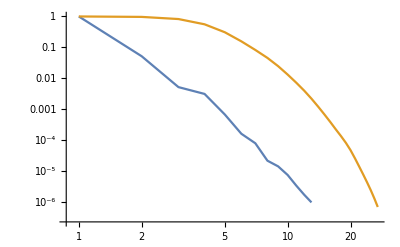

```mathematica
ListLinePlot[{resultLeft["ResidualHistory"],resultRight["ResidualHistory"]},ScalingFunctions->{"Log","Log"}]
```

```mathematica
Dataset[resultLeft]
Dataset[resultRight]
```

```mathematica
(*xGMRES=SparseArray`KrylovLinearSolve[A,b,MaxIterations->maxiter,Tolerance->TOL];//AbsoluteTiming
Norm[A[xGMRES]-b]/Norm[b]
Norm[P[A[xGMRES]-b]]/Norm[P[b]]*)

prec[x_]:=P[x];
xPGMRES=SparseArray`KrylovLinearSolve[A,b,"Preconditioner"->prec,MaxIterations->maxiter,Tolerance->TOL];//AbsoluteTiming
Norm[A[xPGMRES]-b]/Norm[b]
Norm[P[A[xPGMRES]-b]]/Norm[P[b]]
error[xPGMRES]
```

{0.110085,Null}

9.99525×10^-7

2.90015×10^-10

4.02264×10^-8

```mathematica
resultCG=CGLinearSolve[A,b,"Preconditioner"->P,MaxIterations->maxiter,Tolerance->TOL,"ResidualType"->"Preconditioner"];
xCG=resultCG["Solution"];
Norm[A[xCG]-b]/Norm[b]
Norm[P[A[xCG]-b]]/Norm[P[b]]
error[xCG]
```

0.0000255744

3.14134×10^-7

1.07136×10^-6

```mathematica
Dataset[resultCG]
```

```mathematica
Dataset[resultLeft]
```